```mathematica
$Assumptions={_∈Reals, h > 0, Vt > 0, d  > 0, A > 0};
	
TProduct[M__]:=KroneckerProduct[M]
σI = PauliMatrix[0];
σX = PauliMatrix[1];
σY = PauliMatrix[2];
σZ = PauliMatrix[3];
X = σX;
Y = σY;
Z = σZ;
σII = TProduct[σI, σI];
σIX = TProduct[σI, σX];
σIY = TProduct[σI, σY];
σIZ = TProduct[σI, σZ];
σXI = TProduct[σX, σI];
σXX = TProduct[σX, σX];
σXY = TProduct[σX, σY];
σXZ = TProduct[σX, σZ];
σYI = TProduct[σY, σI];
σYX = TProduct[σY, σX];
σYY = TProduct[σY, σY];
σYZ = TProduct[σY, σZ];
σZI = TProduct[σZ, σI];
σZX = TProduct[σZ, σX];
σZY = TProduct[σZ, σY];
σZZ = TProduct[σZ, σZ];

printAsPauliMatrices[M_] := (
σs = {σI, σX, σY, σZ};
letters = {"I", "X", "Y", "Z"};
output = {};
If[Length[M] == 2,(
Do[
term =  Total[Total[Conjugate[σs[[i]]]*M]]/Length[M];
If[!PossibleZeroQ[term],
output = Join[output, {ToString[term // FullSimplify, StandardForm], " σ", letters[[i]], " + "}];
];
,{i, 4}]
)];
If[Length[M] == 4, (
Do[
Do[
term =  Total[Total[Conjugate[TProduct[σs[[i]], σs[[j]]]]*M]]/Length[M] // FullSimplify;
If[!PossibleZeroQ[term],
output = Join[output, {ToString[term, StandardForm], " σ", letters[[i]], letters[[j]],  " + "}];
];
,{i, 4}];
,{j, 4}];
)];

Print[StringJoin[output[[;;Length[output] - 1]]]];
)

printWithBasis[M_,states_]:=(ML=Length[M];
newM=Table[If[(i==0&&j≠0),states[[j]],If[j==0&&i≠0,states[[i]],If[i==0&&j==0,"",M[[i]][[j]]]]],{i,0,ML},{j,0,ML}];
Print[MatrixForm[newM]])

stateString[state_, basis_, cutoff_:0] := (
output = {};
Do[
term = state[[i]];
If[Abs[term] > cutoff,
output = Join[output, {ToString[term], basis[[i]], " + "}]
];
,{i, Length[state]}];
StringJoin[output[[;;Length[output] - 1]]]
)


basisID = {"|i↓⇓>", "|i↓⇑>", "|i↑⇓>", "|i↑⇑>", "|d↓⇓>", "|d↓⇑>", "|d↑⇓>", "|d↑⇑>"};
basisGE = {"|g↓⇓>", "|g↓⇑>", "|g↑⇓>", "|g↑⇑>", "|e↓⇓>", "|e↓⇑>", "|e↑⇓>", "|e↑⇑>"};

Sx=(hBar/2)σX;
Sy=(hBar/2)σY;
Sz=(hBar/2)σZ;

Ix=(hBar/2)σX;
Iy=(hBar/2)σY;
Iz=(hBar/2)σZ;

SdotI=TProduct[Sx,Ix]+TProduct[Sy,Iy]+TProduct[Sz,Iz];

hBar=1;

transform[M_,U_]:=U.M.ConjugateTranspose[U]-ⅈ*hBar*U.ConjugateTranspose[D[U, t]]

(* SI units *)
setVariables[]:=(
B0=.2; (* T *)
d=15*10^-9; (* m *)
Bac=.0006; (* T *)
Eac = 0; (* V/m *)
A=117*10^6; (* Hz *)
γe=27.97*10^9; (* Hz/T *)
γn=17.23*10^6; (* Hz/T *)
Δγ=-.002;
h=6.62607004*10^-34; (* J*s *)
e=-1.60217662*10^-19; (* C *)
Vt = γe*B0 + A/4; (* Hz *)
νB = γe*B0 + A/4; (* Hz *)
νE = (γe + γn)*B0; (* Hz *)
δB = γe*B0 - νB;
)

ϵ0 = √(Vt^2+(d^2 e^2 ΔE^2)/h^2);

clearVariables[]:=Clear[B0,Bac,νB, νE, γe,γn,Δγ,A,Aac,ΔE,Eac,Vt,d,h, e, δB, δE, δ]
```

```mathematica
HorbBase = Vt/2 σX-((e*ΔE*d)/(2h))σZ;
{β, α} = Eigensystem[HorbBase][[2]][[2]] // Normalize // FullSimplify;
α = -α;

iState = {α, β};
dState = {β, -α};
ii = Outer[Times, iState, iState] // FullSimplify;
id = Outer[Times, iState, dState] // FullSimplify;
di = Outer[Times, dState, iState] // FullSimplify;
dd = Outer[Times, dState, dState] // FullSimplify;

HB0=-B0 (γe*TProduct[(σI+Δγ*dd),Sz, σI]-γn*TProduct[σI,σI, Iz]);
HA=TProduct[A*dd,SdotI];
Horb=TProduct[-((e*(ΔE + Eac*Cos[2*π*νE*t])*d)/(2h))*(ii - dd) + (Vt/2)(id + di), σI, σI];
HESR = Bac*Sin[2*π*νB*t](γe*TProduct[σI,Sx, σI]-γn*TProduct[σI,σI, Ix]);

HnsInGE = -δB*TProduct[σI, Sz, σI] + (γn*B0 + νB)*TProduct[σI, σI, Iz] + (Bac/2)(γe*TProduct[σI, Sx, σI] - γn*TProduct[σI, σI, Ix]) + Horb + HA;

H = HB0 + HESR + HA + Horb;

energiesAt[Ef_, M_] := Eigensystem[M /. {ΔE -> Ef}][[1]]
energiesInOrder[Ef_, M_] := energiesAt[Ef, M][[order[Ef, M]]]
statesAt[Ef_, M_] := Eigensystem[M /. {ΔE -> Ef}][[2]]
statesInOrder[Ef_, M_] := statesAt[Ef, M][[order[Ef, M]]]

targetStates = IdentityMatrix[8];
order[Ef_, M_] := Table[Ordering[row, -1][[1]], {row,Abs[targetStates.ConjugateTranspose[statesAt[Ef, M]]]}]
putInOrder[Q_, Ef_, M_] := Q[[order[Ef, M]]]
```

```mathematica
(* PLOT EVOLUTION UNDER DRIVING FIELDS *)
```

2.11667×10^-6

0.

{0.999991,2.47951×10^-37,2.21461×10^-35,0.,9.03306×10^-6,3.37014×10^-36,0.,0.}

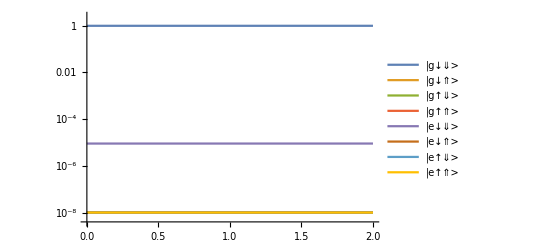

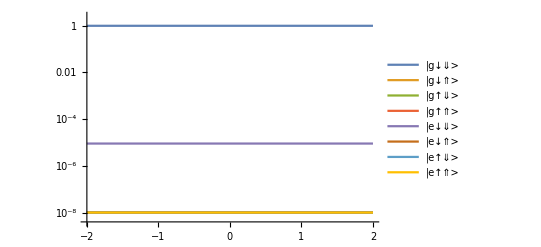

```mathematica
Tmax = 100*10^-9;

Clear[findEvolution];
findEvolution[ΔEin_?NumericQ, B0in_?NumericQ, Eacin_?NumericQ, Bacin_?NumericQ, δEin_?NumericQ, δBin_?NumericQ] := (
setVariables[];
Clear[Eff, EeSpin, EnSpin, undrivenStates, ψ0, funcs, equations, state];

ΔE = ΔEin;
B0 = B0in;

Bac = 0;
Eac = 0;

Eff = (energiesInOrder[0, H][[3]] - energiesInOrder[0, H][[2]]);
EeSpin = (energiesInOrder[0, H][[3]] - energiesInOrder[0, H][[1]]);
undrivenStates = statesInOrder[0, H];

Bac = Bacin;
Eac = Eacin;
νB = (EeSpin - δBin);
νE = (Eff - δEin);

M = 2*π*H;

ψ0 = undrivenStates[[1]];

funcs=Array[ψ[#1][t]&,{Length[ψ0]}];

equations=Flatten@Join[Thread[M.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];

state= NDSolveValue[equations,funcs,{t,-Tmax/100,101*Tmax/100}];

clearVariables[];
Clear[Eff, EeSpin, EnSpin, undrivenStates, ψ0, funcs, equations];

state
)

averageBits = (Tmax/1000)*RandomReal[{-5, 5}, 100];

bestSoFar = 0;
bestT = 0;
bestParameters = {};

Clear[maxGDUcoefficient];
maxGDUcoefficient[ΔEin_?NumericQ, B0in_?NumericQ, Eacin_?NumericQ, Bacin_?NumericQ, δE_?NumericQ, δB_?NumericQ] := (
state = findEvolution[ΔEin, B0in, Eacin, Bacin, δE, δB];
state = Abs[state]^2;

ts = Table[t, {t, 0, Tmax, Tmax/1000}];
otherSum = state[[1]] + state[[3]] + state[[4]] + state[[5]] + state[[6]] + state[[7]] + state[[8]];
samples = Table[1 - Sum[(otherSum) /.{t->(tt + dt)}, {dt, averageBits}]/Length[averageBits], {tt, 0, Tmax, Tmax/1000}];
maxSample = Max[samples];

If[maxSample > bestSoFar, (bestSoFar = maxSample; bestParameters = {ΔEin, B0in, Eacin, Bacin, δE, δB}; bestT = N[ts[[Ordering[samples, -1]]][[1]]]; (*Print[{bestSoFar, bestParameters}]*))];

maxSample
)

bestSoFar = 0;
bestT = 0;
bestParameters = {};

Tmax = Tmax*2;
(*maxGDUcoefficient[0, .8*.2*1.0056, 200, .0007, 2*10^7, 2*10^7]*)
maxGDUcoefficient[-68.63253962234526,0.1654317731042863,0*124.96366462898797,0*0.0005183252929544237,-171728.42293817864,-171728.42293817864]
bestT
state /. {t->bestT}
LogPlot[Evaluate@Table[Max[state[[i]], 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->basisGE]
LogPlot[Evaluate@Table[Max[state[[i]], 10^-8], {i, Length[state]}],{t,bestT - Tmax/1000, bestT + Tmax/1000}, PlotRange->All, PlotLegends->basisGE]
Tmax = Tmax/2;
```

```mathematica
setVariables[];
Clear[Eff, EeSpin, EnSpin, undrivenStates, undrivenEnergies, ψ0, funcs, equations, state, α, β];

ΔE = 50.09011359258564;
B0 = 0.16424778120598266;

Bac = 0;
Eac = 0;

Eff = (energiesInOrder[0, H][[3]] - energiesInOrder[0, H][[2]]);
EeSpin = (energiesInOrder[0, H][[3]] - energiesInOrder[0, H][[1]]);
undrivenEnergies = energiesInOrder[0, H]
drivenEnergies = energiesInOrder[0, HnsInGE]

Bac = 0.00025523343867387636;
Eac = 59.04708726440646;
νB = (EeSpin - 9.955468751323821*^6);
νE = (Eff - 9.955468751323821*^6);

gSO = (A*Vt)/(4*ϵ0)
gB = γe*Bac
gE = (e*Eac*d*Vt)/(4*h*ϵ0)
δSO = ϵ0 - Eff
δ1 = drivenEnergies[[3]] - drivenEnergies[[1]]
δ2 = drivenEnergies[[6]] - drivenEnergies[[1]];;
δ3 = drivenEnergies[[4]] - drivenEnergies[[2]];

ϕ = (δSO + Sqrt[δSO^2 + 4*gSO^2])/(2*gSO);
θ = (δSO - Sqrt[δSO^2 + 4*gSO^2])/(2*gSO);

α = θ/Sqrt[θ^2 + 1];
β = ϕ/Sqrt[ϕ^2 + 1];

ϕ3 = (δ3 + Sqrt[δ3^2 + 4*gB^2])/(2*gB);
θ1 = (δ1 - Sqrt[δ1^2 + 4*β^2*gB^2])/(2*β*gB);
θ2 = (δ2 - Sqrt[δ2^2 + 4*α^2*gB^2])/(2*α*gB);

α1 = θ1/Sqrt[θ1^2 + 1];
α2 = θ2/Sqrt[θ2^2 + 1];
β3 = ϕ3/Sqrt[ϕ3^2 + 1];

gEns = gE*β3(α1*α + α2*β);

LogPlot[Max[10^-8, Sin[gEns*t]^2], {t, 0, Tmax}]
```

{-5.09126×10^9,-5.12455×10^9,-5.32817×10^8,-5.04803×10^8,5.33928×10^8,5.03423×10^8,5.09544×10^9,5.12064×10^9}

{2.96323×10^7,-5.62688×10^9,-4.74814×10^7,-5.6257×10^9,5.65495×10^9,1.82543×10^7,5.59761×10^9,-382254.}

2.92347×10^7

7.13888×10^6

-5.35128×10^7

1.03445×10^9

-7.71136×10^7

Set::write: Tag Span in -1.1378×10^7;;δ3 is Protected.

-Graphics-